```mathematica
Num = 100; dx = 1./(Num+1);
```

```mathematica
Potential[x_]:=If[x>.25&&x<.75,-20,0];
```

```mathematica
D1=1/(2dx)Table[If[i==j+1,1,If[i==j-1,-1,0]],{i,1,Num},{j,1,Num}];
D1[[1,Num]]=1/(2dx);
D1[[Num,1]]=-1/(2dx);
```

```mathematica
D2=1/dx^2 Table[If[i==j,-2,If[i==j+1,1,If[i==j-1,1,0]]],{i,1,Num},{j,1,Num}];
D2[[1,Num]]=D2[[Num,1]]=1/dx^2;
```

```mathematica
V=Table[If[i==j,Potential[i dx],0],{i,1,Num},{j,1,Num}];
```

```mathematica
Energy[q_,n_]:=q^2-Sort[Eigenvalues[D2+2ⅈ q D1-V]//Chop][[Num+1-n]]
```

```mathematica
TableForm[Table[Energy[q,n],{n,1,2},{q,{-π,-π/2,0,π/2,π}}],TableHeadings->{{1,2},{-π,-π/2,0,π/2,π}}]
```

| -π | -π/2 | 0 | π/2 | π
1 | -6.77261 | -10.0067 | -11.9549 | -10.0067 | -6.77261
2 | 5.84137 | 14.1147 | 29.6386 | 14.1147 | 5.84137

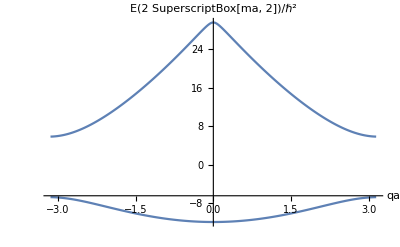

```mathematica
Show[ListPlot[Table[{q,Energy[q,1]},{q,-π,π,π/100}],Joined->True],ListPlot[Table[{q,Energy[q,2]},{q,-π,π,π/100}],Joined->True],PlotRange->All,AxesLabel->{"qa","E(2 SuperscriptBox[ma, 2])/ℏ^2"}]
```